# PicoVNA .dat analyser Anna Migó – December 2023

## 1. Preamble

This notebook i) reads in the data from a VNA .dat file (output format from the picoVNA: “Real+Imag”), then ii) transforms the S parameters into the Z (impedance), Y (admittance), H (hybrid) and G (inverse hybrid) parameters and plots them as functions of frequency and then iii) plots the S, Z, Y, H and G parameters

Contents
Section 1. Preamble - this is where the user inputs are: Only modify the name of the folder/file
Section 2. Importing the raw data from the dat file.
Section 3. Defining functions to transform S into Z, and Y.
Section 4. Perform the transformations.
Section 5. Plotting the real and imaginary parts of S, Z, Y.
Section 6. Plotting the magnitude and phase of S, Z, Y.

### 0.1 User inputs (change these)

```mathematica
NameFolderToImport="Measures_SF"; (* Set the foldername  *)
NameFileToImport="s.f_example" ;(* Set the filename while omitting the ".dat" extension *)
```

### 0.2 Not user inputs (do not change these)

```mathematica
Address=NotebookDirectory[]<>NameFolderToImport<>"/"<>NameFileToImport; (* directory name *)

ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ=16; (* Set the font size for plots *) 
ℐ𝓂𝒶ℊℯ𝒮𝒾𝓏ℯ=400; (* Set the plot size for plots *) 
ℱ𝓇ℯ𝓆𝒰𝓃𝒾𝓉𝓈𝒮𝒯ℛ="MHz"; (* Set the desired frequency units "kHz" or "MHz" or "Ghz"; only for the plots - the produced .txt files still include units of Hz *)
𝒵01 = 50;(* Set the input impedance of port 1; units ohms *) 
𝒵02 = 50;(* Set the input impedance of port 2; units ohms *) 

ℱ𝓇ℯ𝓆𝒰𝓃𝒾𝓉𝓈ℳ𝓊ℓ𝓉 = Which[ℱ𝓇ℯ𝓆𝒰𝓃𝒾𝓉𝓈𝒮𝒯ℛ=="Hz",10^-6,ℱ𝓇ℯ𝓆𝒰𝓃𝒾𝓉𝓈𝒮𝒯ℛ=="kHz",10^-3,ℱ𝓇ℯ𝓆𝒰𝓃𝒾𝓉𝓈𝒮𝒯ℛ=="MHz",10^0,ℱ𝓇ℯ𝓆𝒰𝓃𝒾𝓉𝓈𝒮𝒯ℛ=="GHz",10^3]; (* Sets the frequency muiltiplier ℱ𝓇ℯ𝓆𝒰𝓃𝒾𝓉𝓈ℳ𝓊ℓ𝓉 based upon the desired frequency units; the reference has been set in MHz, as the data from the picoVNA is saved in MHz *) 
𝒴01 = 1/𝒵01; (* Input admittance of port 1; units S *) 
𝒴02 = 1/𝒵02; (* Input admittance of port 2; units S *)
```

## 2. Importing the raw data from the .dat file (get S parameters)

### 1.1 Import the file and transform it into 9 different columns, {freq}{ReS11}{ImS11}...S21, S12,S22

```mathematica
AllDataTable=Import[Address<>".dat","Table"];
```

```mathematica
S11ArrayFreqRealImag=Transpose[AllDataTable[[All,{1,2,3}]]]//MatrixForm;
S21ArrayFreqRealImag=Transpose[AllDataTable[[All,{1,4,5}]]]//MatrixForm;
S12ArrayFreqRealImag=Transpose[AllDataTable[[All,{1,6,7}]]]//MatrixForm;
S22ArrayFreqRealImag=Transpose[AllDataTable[[All,{1,8,9}]]]//MatrixForm;
(* Table of data for {ν(MHz),Re[Subscript[S, 11]],Im[Subscript[S, 11]]} en columnies*)
```

## 3. Defining functions to calculate alternative parameters

These functions (“Two-Port Network Matrix conversions”) were copied and pasted from “JFET Amplifier Functions.nb”.

## Two-Port Network Matrix conversions

```mathematica
ConvertZtoABCD[Z_]:=({{Z⟦1,1⟧/Z⟦2,1⟧, (Z⟦1,1⟧Z⟦2,2⟧)/Z⟦2,1⟧-Z⟦1,2⟧}, {1/Z⟦2,1⟧, Z⟦2,2⟧/Z⟦2,1⟧}});
```

```mathematica
ConvertABCDtoZ[A_]:=({{A⟦1,1⟧/A⟦2,1⟧, (A⟦1,1⟧A⟦2,2⟧)/A⟦2,1⟧-A⟦1,2⟧}, {1/A⟦2,1⟧, A⟦2,2⟧/A⟦2,1⟧}});
```

```mathematica
ConvertYtoABCD[Y_]:=({{-Y⟦2,2⟧/Y⟦2,1⟧, -1/Y⟦2,1⟧}, {Y⟦1,2⟧-(Y⟦1,1⟧Y⟦2,2⟧)/Y⟦2,1⟧, -Y⟦1,1⟧/Y⟦2,1⟧}});
```

```mathematica
ConvertABCDtoY[A_]:=({{A⟦2,2⟧/A⟦1,2⟧, A⟦2,1⟧-(A⟦1,1⟧A⟦2,2⟧)/A⟦1,2⟧}, {-1/A⟦1,2⟧, A⟦1,1⟧/A⟦1,2⟧}});
```

```mathematica
ConvertABCDtoh[A_]:=({{A⟦1,2⟧/A⟦2,2⟧, A⟦1,1⟧-(A⟦1,2⟧A⟦2,1⟧)/A⟦2,2⟧}, {-1/A⟦2,2⟧, A⟦2,1⟧/A⟦2,2⟧}});
```

```mathematica
ConverthtoABCD[h_]:=({{h⟦1,2⟧-(h⟦1,1⟧h⟦2,2⟧)/h⟦2,1⟧, -h⟦1,1⟧/h⟦2,1⟧}, {-h⟦2,2⟧/h⟦2,1⟧, -1/h⟦2,1⟧}});
```

```mathematica
ConvertABCDtog[A_]:=({{A⟦2,1⟧/A⟦1,1⟧, (A⟦1,2⟧A⟦2,1⟧)/A⟦1,1⟧-A⟦2,2⟧}, {1/A⟦1,1⟧, A⟦1,2⟧/A⟦1,1⟧}});
```

```mathematica
ConvertgtoABCD[g_]:=({{1/g⟦2,1⟧, g⟦2,2⟧/g⟦2,1⟧}, {g⟦1,1⟧/g⟦2,1⟧, (g⟦1,1⟧g⟦2,2⟧)/g⟦2,1⟧-g⟦1,2⟧}});
```

```mathematica
ConvertZtoS[Z_,Z01_,Z02_]:=({{(Z⟦1,2⟧ Z⟦2,1⟧+(Z01-Z⟦1,1⟧) (Z02+Z⟦2,2⟧))/(Z⟦1,2⟧ Z⟦2,1⟧-(Z01+Z⟦1,1⟧) (Z02+Z⟦2,2⟧)), (2 Z01 Z⟦1,2⟧)/(-Z⟦1,2⟧ Z⟦2,1⟧+(Z01+Z⟦1,1⟧) (Z02+Z⟦2,2⟧))}, {(2 Z02 Z⟦2,1⟧)/(-Z⟦1,2⟧ Z⟦2,1⟧+(Z01+Z⟦1,1⟧) (Z02+Z⟦2,2⟧)), (Z⟦1,2⟧ Z⟦2,1⟧+(Z01+Z⟦1,1⟧) (Z02-Z⟦2,2⟧))/(Z⟦1,2⟧ Z⟦2,1⟧-(Z01+Z⟦1,1⟧) (Z02+Z⟦2,2⟧))}});
```

```mathematica
ConvertStoZ[S_,Z01_,Z02_]:=({{(Z01 (-1-S⟦1,2⟧ S⟦2,1⟧+S⟦1,1⟧ (-1+S⟦2,2⟧)+S⟦2,2⟧))/(-1+S⟦1,2⟧ S⟦2,1⟧-S⟦1,1⟧ (-1+S⟦2,2⟧)+S⟦2,2⟧), -(2 S⟦1,2⟧Z02)/(-1+S⟦1,2⟧ S⟦2,1⟧-S⟦1,1⟧ (-1+S⟦2,2⟧)+S⟦2,2⟧)}, {-(2 Z01 S⟦2,1⟧)/(-1+S⟦1,2⟧ S⟦2,1⟧-S⟦1,1⟧ (-1+S⟦2,2⟧)+S⟦2,2⟧), (Z02 (1+S⟦1,2⟧ S⟦2,1⟧+S⟦2,2⟧-S⟦1,1⟧ (1+S⟦2,2⟧)))/(1-S⟦1,2⟧ S⟦2,1⟧+S⟦1,1⟧ (-1+S⟦2,2⟧)-S⟦2,2⟧)}});
```

```mathematica
ConvertStoY[S_,Y01_,Y02_]:=({{(Y01 (S⟦1,2⟧ S⟦2,1⟧+S⟦2,2⟧ -S⟦1,1⟧(S⟦2,2⟧+1)+1))/(1-S⟦1,2⟧ S⟦2,1⟧+S⟦2,2⟧+S⟦1,1⟧ (S⟦2,2⟧+1)), -(2 S⟦1,2⟧Y01)/(1-S⟦1,2⟧ S⟦2,1⟧+S⟦2,2⟧+S⟦1,1⟧ (S⟦2,2⟧+1))}, {-(2 Y02 S⟦2,1⟧)/(1-S⟦1,2⟧ S⟦2,1⟧+S⟦2,2⟧+S⟦1,1⟧ (S⟦2,2⟧+1)), -(Y02 (-S⟦1,2⟧ S⟦2,1⟧+S⟦2,2⟧+S⟦1,1⟧ (S⟦2,2⟧-1)-1))/(1-S⟦1,2⟧ S⟦2,1⟧+S⟦2,2⟧+S⟦1,1⟧ (S⟦2,2⟧+1))}});
```

```mathematica
ConvertYtoS[Y_,Y01_,Y02_]:=({{(Y⟦1,2⟧ Y⟦2,1⟧+(Y01-Y⟦1,1⟧)(Y02+Y⟦2,2⟧))/((Y01+Y⟦1,1⟧)(Y02+Y⟦2,2⟧)-Y⟦1,2⟧ Y⟦2,1⟧), -(2 Y02 Y⟦1,2⟧)/((Y01+Y⟦1,1⟧)(Y02+Y⟦2,2⟧)-Y⟦1,2⟧ Y⟦2,1⟧)}, {-(2 Y01 Y⟦2,1⟧)/((Y01+Y⟦1,1⟧)(Y02+Y⟦2,2⟧)-Y⟦1,2⟧ Y⟦2,1⟧), (Y⟦1,2⟧ Y⟦2,1⟧+(Y01+Y⟦1,1⟧)(Y02-Y⟦2,2⟧))/((Y01+Y⟦1,1⟧)(Y02+Y⟦2,2⟧)-Y⟦1,2⟧ Y⟦2,1⟧)}});
```

```mathematica
ConvertZtoG[Z_]:=({{1/Z⟦1,1⟧, -Z⟦1,2⟧/Z⟦1,1⟧}, {Z⟦2,1⟧/Z⟦1,1⟧, Z⟦2,2⟧-(Z⟦1,2⟧*Z⟦2,1⟧)/Z⟦1,1⟧}});
```

```mathematica
ConvertZtoH[Z_]:=({{Z⟦1,1⟧-(Z⟦1,2⟧*Z⟦2,1⟧)/Z⟦2,2⟧, Z⟦1,2⟧/Z⟦2,2⟧}, {-Z⟦2,1⟧/Z⟦2,2⟧, 1/Z⟦2,2⟧}});
```

```mathematica
ConvertYtoH[Y_]:=({{1/Y⟦1,1⟧, -Y⟦1,2⟧/Y⟦1,1⟧}, {Y⟦2,1⟧/Y⟦1,1⟧, Y⟦2,2⟧-(Y⟦1,2⟧*Y⟦2,1⟧)/Y⟦1,1⟧}});
```

```mathematica
ConvertYtoG[Y_]:=({{Y⟦1,1⟧-(Y⟦1,2⟧*Y⟦2,1⟧)/Y⟦2,2⟧, Y⟦1,2⟧/Y⟦2,2⟧}, {-Y⟦2,1⟧/Y⟦2,2⟧, 1/Y⟦2,2⟧}});
```

## 4. Transforming into alternative parameters

```mathematica
(* The elements of each matrix M are defined by ({{Subscript[M, 11], Subscript[M, 12]}, {Subscript[M, 21], Subscript[M, 22]}}), in keeping with the functions("Two-Port Network Matrix conversions") in Section 3 above which were copied from "JFET Amplifier Functions.nb" *)
```

```mathematica
ElementsIntoMatrix[M11Re_, M11Im_,M21Re_, M21Im_,M12Re_, M12Im_,M22Re_, M22Im_]:=MatrixForm[{{M11Re+I*M11Im,M12Re+I*M12Im},{M21Re+I*M21Im,M22Re+I*M22Im}}] (* Puts the real and imaginary parts of the elements of a matrix into a single matrix *)
```

```mathematica
ArrayFrequencies=Transpose[Table[S11ArrayFreqRealImag⟦i⟧⟦1⟧,{i,1,Length[S11ArrayFreqRealImag]}]]//MatrixForm;(* Array {Subscript[ν, i-1], Subscript[ν, i], Subscript[ν, i+1], ... Subscript[ν, N]}; units MHz *)
```

```mathematica
ArraySMatrices=Table[ElementsIntoMatrix[S11ArrayFreqRealImag⟦1⟧⟦2,i⟧,S11ArrayFreqRealImag⟦1⟧⟦3,i⟧,S21ArrayFreqRealImag⟦1⟧⟦2,i⟧,S21ArrayFreqRealImag⟦1⟧⟦3,i⟧,S12ArrayFreqRealImag⟦1⟧⟦2,i⟧,S12ArrayFreqRealImag⟦1⟧⟦3,i⟧,S22ArrayFreqRealImag⟦1⟧⟦2,i⟧,S22ArrayFreqRealImag⟦1⟧⟦3,i⟧],{i,1,Length[ArrayFrequencies[[1]]]}]//MatrixForm(* Array {Smatrix at Subscript[ν, i-1], Smatrix at Subscript[ν, i], Smatrix at Subscript[ν, i+1], ... Smatrix at Subscript[ν, N]}; units dimensionless *);
```

```mathematica
ArrayZMatrices = Table[ConvertStoZ[ArraySMatrices⟦1⟧⟦i⟧[[1]],𝒵01,𝒵02],{i,1,Length[ArrayFrequencies[[1]]]}]//MatrixForm;(* Array {Zmatrix at Subscript[ν, i-1], Zmatrix at Subscript[ν, i], Zmatrix at Subscript[ν, i+1], ... Zmatrix at Subscript[ν, N]}; units ohms *)
ArrayYMatrices = Table[ConvertStoY[ArraySMatrices⟦1⟧⟦i⟧[[1]],𝒴01,𝒴02],{i,1,Length[ArrayFrequencies[[1]]]}]//MatrixForm;(* Array {Ymatrix at Subscript[ν, i-1], Ymatrix at Subscript[ν, i], Ymatrix at Subscript[ν, i+1], ... Ymatrix at Subscript[ν, N]}; units S *)
ArrayHMatrices = Table[ConvertZtoH[ArrayZMatrices⟦1⟧⟦i⟧],{i,1,Length[ArrayZMatrices[[1]]]}]//MatrixForm;(* Array {Hmatrix at Subscript[ν, i-1], Hmatrix at Subscript[ν, i], Hmatrix at Subscript[ν, i+1], ... Hmatrix at Subscript[ν, N]}; units various *)
ArrayGMatrices = Table[ConvertZtoG[ArrayZMatrices⟦1⟧⟦i⟧],{i,1,Length[ArrayZMatrices[[1]]]}]//MatrixForm;(* Array {Gmatrix at Subscript[ν, i-1], Gmatrix at Subscript[ν, i], Gmatrix at Subscript[ν, i+1], ... Gmatrix at Subscript[ν, N]}; units various *)
```

## 5. Plotting the real and imaginary parts of S_nm, Z_nm, Y_nm, H_nm, G_nm as functions of the frequency ν

### 5.1 Defining a functions to plot (Re[S_nm] and Im[S_nm]) or (Re[M_nm] and Im[M_nm]) as functions of the frequency

```mathematica
PlotSnmFunctionReIm[FrequenciesArray_,MnmArray_,MnmStr_,n_,m_]:={MnmArrayTableRe=Table[{(FrequenciesArray⟦i⟧[[1]])/ℱ𝓇ℯ𝓆𝒰𝓃𝒾𝓉𝓈ℳ𝓊ℓ𝓉,Re[MnmArray⟦i,1⟧⟦n,m⟧]},{i,1,Length[FrequenciesArray]}]; (* Array {Subscript[ν, i], Re[Subscript[M, i]]} *)
MnmArrayTableIm=Table[{(FrequenciesArray⟦i⟧[[1]])/ℱ𝓇ℯ𝓆𝒰𝓃𝒾𝓉𝓈ℳ𝓊ℓ𝓉,Im[MnmArray⟦i,1⟧⟦n,m⟧]},{i,1,Length[FrequenciesArray]}]; (* Array {Subscript[ν, i], Im[Subscript[M, i]]} *)
PlotMnmReVsFreq= ListPlot[MnmArrayTableRe,PlotStyle->{Blue,Thickness[0.004]},Joined->True,AxesStyle->Directive[Black,ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ],AxesLabel->{Style["ω/(2  π) ("<>ToString[ℱ𝓇ℯ𝓆𝒰𝓃𝒾𝓉𝓈𝒮𝒯ℛ]<> ")",ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ,Black],Style[MnmStr<>" (dimensionless)",ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ,Black]},PlotRange->All,PlotLegends-> LineLegend[{"Re["<>MnmStr<>"]"}]];
PlotMnmImVsFreq = ListPlot[MnmArrayTableIm,PlotStyle->{Red,Thickness[0.004]},Joined->True,AxesStyle->Directive[Black,ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ],AxesLabel->{Style["ω/(2  π) ("<>ToString[ℱ𝓇ℯ𝓆𝒰𝓃𝒾𝓉𝓈𝒮𝒯ℛ]<> ")",ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ,Black],Style[MnmStr<>" (dimensionless)",ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ,,Black]},PlotRange->All,PlotLegends-> LineLegend[{"Im["<>MnmStr<>"]"}]];
Show[{PlotMnmReVsFreq,PlotMnmImVsFreq},PlotRange->All,ImageSize->ℐ𝓂𝒶ℊℯ𝒮𝒾𝓏ℯ]}⟦1⟧ (* Defining a function to plot the real and imaginary parts of one element of a scattering matrix as functions of frequency *)
```

```mathematica
PlotMnmFunctionReIm[FrequenciesArray_,MnmArray_,MnmStr_,n_,m_,UnitsStr_]:={MnmArrayTableRe=Table[{(FrequenciesArray⟦i⟧[[1]])/ℱ𝓇ℯ𝓆𝒰𝓃𝒾𝓉𝓈ℳ𝓊ℓ𝓉,Re[MnmArray⟦i⟧⟦n,m⟧]},{i,1,Length[FrequenciesArray]}]; (* Array {Subscript[ν, i], Re[Subscript[M, i]]} *)
MnmArrayTableIm=Table[{(FrequenciesArray⟦i⟧[[1]])/ℱ𝓇ℯ𝓆𝒰𝓃𝒾𝓉𝓈ℳ𝓊ℓ𝓉,Im[MnmArray⟦i⟧⟦n,m⟧]},{i,1,Length[FrequenciesArray]}]; (* Array {Subscript[ν, i], Im[Subscript[M, i]]} *)
PlotMnmReVsFreq= ListPlot[MnmArrayTableRe,PlotStyle->{Blue,Thickness[0.004]},Joined->True,AxesStyle->Directive[Black,ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ],AxesLabel->{Style["ω/(2  π) ("<>ToString[ℱ𝓇ℯ𝓆𝒰𝓃𝒾𝓉𝓈𝒮𝒯ℛ]<> ")",ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ,Black],Style[MnmStr<>" "<>UnitsStr,ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ,Black]},PlotRange->All,PlotLegends-> LineLegend[{"Re["<>MnmStr<>"]"}]];
PlotMnmImVsFreq = ListPlot[MnmArrayTableIm,PlotStyle->{Red,Thickness[0.004]},Joined->True,AxesStyle->Directive[Black,ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ],AxesLabel->{Style["ω/(2  π) ("<>ToString[ℱ𝓇ℯ𝓆𝒰𝓃𝒾𝓉𝓈𝒮𝒯ℛ]<> ")",ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ,Black],Style[MnmStr<>" "<>UnitsStr,ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ,,Black]},PlotRange->All,PlotLegends-> LineLegend[{"Im["<>MnmStr<>"]"}]];
Show[{PlotMnmReVsFreq,PlotMnmImVsFreq},PlotRange->All,ImageSize->ℐ𝓂𝒶ℊℯ𝒮𝒾𝓏ℯ]}⟦1⟧ (* Defining a function to plot the real and imaginary parts of one element of a transformed matrix as functions of frequency *)
```

### 5.2 Plotting the parameters as functions of frequency

#### 5.2.1 Plotting the S-parameters (scattering parameters)

```mathematica
PlotSnmFunctionReIm[ArrayFrequencies[[1]],ArraySMatrices[[1]],"S_11",1,1] (* Plotting Subscript[S, 11] *)
PlotSnmFunctionReIm[ArrayFrequencies[[1]],ArraySMatrices[[1]],"S_12",1,2] (* Plotting Subscript[S, 12] *) 
PlotSnmFunctionReIm[ArrayFrequencies[[1]],ArraySMatrices[[1]],"S_21",2,1] (* Plotting Subscript[S, 21] *)
PlotSnmFunctionReIm[ArrayFrequencies[[1]],ArraySMatrices[[1]],"S_22",2,2] (* Plotting Subscript[S, 22] *)
```

#### 5.2.2 Plotting the Z-parameters (impedance parameters)

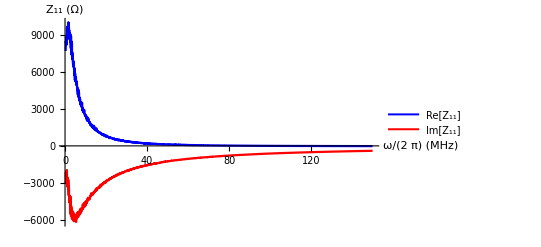

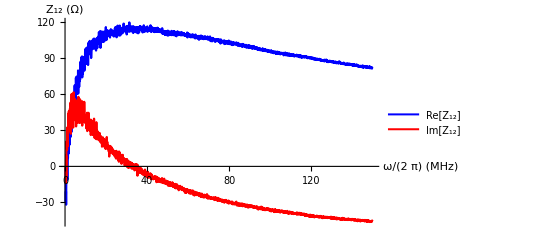

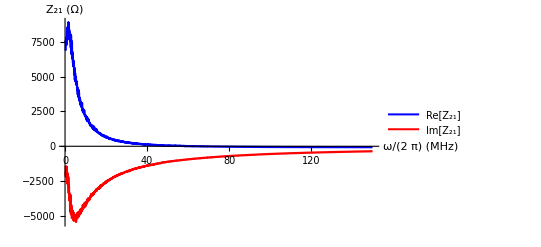

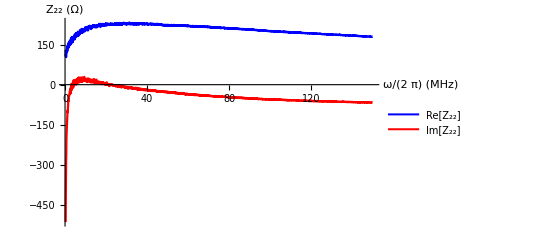

```mathematica
PlotMnmFunctionReIm[ArrayFrequencies[[1]],ArrayZMatrices[[1]],"Z_11",1,1,"(Ω)"] (* Plotting Subscript[Z, 11] *)
PlotMnmFunctionReIm[ArrayFrequencies[[1]],ArrayZMatrices[[1]],"Z_12",1,2,"(Ω)"] (* Plotting Subscript[Z, 12] *) 
PlotMnmFunctionReIm[ArrayFrequencies[[1]],ArrayZMatrices[[1]],"Z_21",2,1,"(Ω)"] (* Plotting Subscript[Z, 21] *) 
PlotMnmFunctionReIm[ArrayFrequencies[[1]],ArrayZMatrices[[1]],"Z_22",2,2,"(Ω)"](* Plotting Subscript[Z, 22] *)
```

#### 5.2.3 Plotting the Y-parameters (admittance parameters)

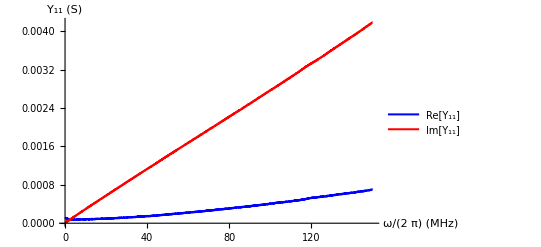

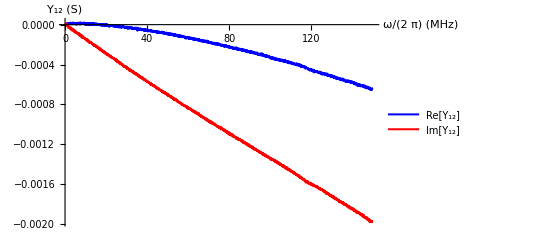

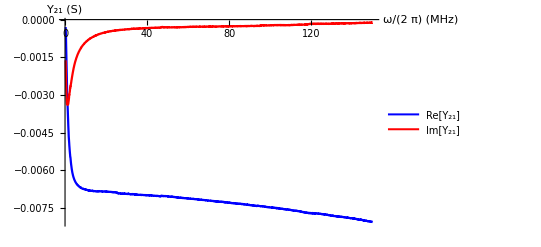

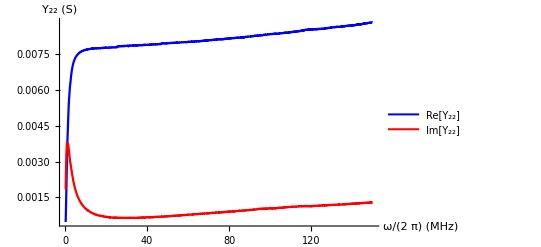

```mathematica
PlotMnmFunctionReIm[ArrayFrequencies[[1]],ArrayYMatrices[[1]],"Y_11",1,1,"(S)"] (* Plotting Subscript[Y, 11] *) 
PlotMnmFunctionReIm[ArrayFrequencies[[1]],ArrayYMatrices[[1]],"Y_12",1,2,"(S)"] (* Plotting Subscript[Y, 12] *) 
PlotMnmFunctionReIm[ArrayFrequencies[[1]],ArrayYMatrices[[1]],"Y_21",2,1,"(S)"] (* Plotting Subscript[Y, 21] *) 
PlotMnmFunctionReIm[ArrayFrequencies[[1]],ArrayYMatrices[[1]],"Y_22",2,2,"(S)"] (* Plotting Subscript[Y, 22] *)
```

#### 5.2.3 Plotting the H-parameters (hybrid parameters)

```mathematica
PlotMnmFunctionReIm[ArrayFrequencies[[1]],ArrayHMatrices[[1]],"H_11",1,1,"(Ω)"] (* Plotting Subscript[H, 11] *) 
PlotMnmFunctionReIm[ArrayFrequencies[[1]],ArrayHMatrices[[1]],"H_12",1,2,"(dimensionless)"] (* Plotting Subscript[H, 12] *) 
PlotMnmFunctionReIm[ArrayFrequencies[[1]],ArrayHMatrices[[1]],"H_21",2,1,"(dimensionless)"] (* Plotting Subscript[H, 21] *) 
PlotMnmFunctionReIm[ArrayFrequencies[[1]],ArrayHMatrices[[1]],"H_22",2,2,"(S)"] (* Plotting Subscript[H, 22] *)
```

#### 5.2.4 Plotting the G-parameters (inverse hybrid parameters)

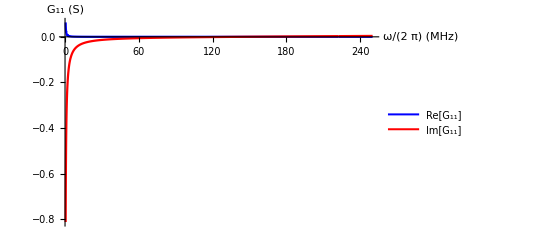

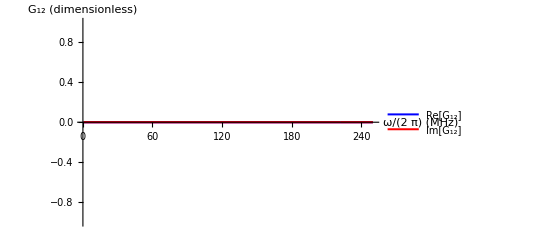

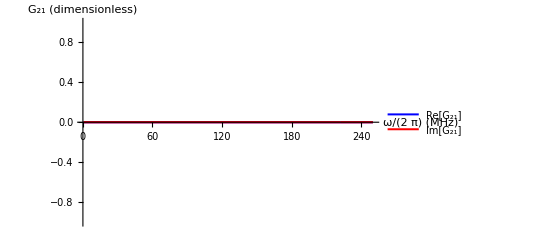

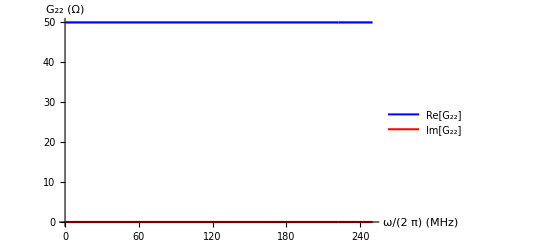

```mathematica
PlotMnmFunctionReIm[ArrayFrequencies[[1]],ArrayGMatrices[[1]],"G_11",1,1,"(S)"] (* Plotting Subscript[G, 11] *) 
PlotMnmFunctionReIm[ArrayFrequencies[[1]],ArrayGMatrices[[1]],"G_12",1,2,"(dimensionless)"] (* Plotting Subscript[G, 12] *) 
PlotMnmFunctionReIm[ArrayFrequencies[[1]],ArrayGMatrices[[1]],"G_21",2,1,"(dimensionless)"] (* Plotting Subscript[G, 21] *) 
PlotMnmFunctionReIm[ArrayFrequencies[[1]],ArrayGMatrices[[1]],"G_22",2,2,"(Ω)"] (* Plotting Subscript[G, 22] *)
```

## 6. Plotting the magnitude and phase of S_nm, Z_nm, Y_nm, H_nm,G_nm as functions of the frequency ν

### 6.1 Defining a functions to plot (Mag[S_nm] and Phase[S_nm]) or (Mag[M_nm] and Phase[M_nm]) as functions of the frequency

Note: arguments: FrequenciesArray_ = array of frequencies , MnmArray_ = array of matrices , MnmStr_ = string to name the element M_nm, n_ = matrix element index n from M_nm, m_ = matrix element index m from S_nm, UnitsStr_ = string of units for M_nm

```mathematica
PlotSnmFunctionMagPhase[FrequenciesArray_,MnmArray_,MnmStr_,n_,m_]:={MnmArrayTableMag=Table[{(FrequenciesArray⟦i⟧[[1]])/ℱ𝓇ℯ𝓆𝒰𝓃𝒾𝓉𝓈ℳ𝓊ℓ𝓉,Abs[MnmArray⟦i,1⟧⟦n,m⟧]},{i,1,Length[FrequenciesArray]}]; (* Array {Subscript[ν, i], Mag[Subscript[M, i]]} *)
MnmArrayTablePhase=Table[{(FrequenciesArray⟦i⟧[[1]])/ℱ𝓇ℯ𝓆𝒰𝓃𝒾𝓉𝓈ℳ𝓊ℓ𝓉,Arg[MnmArray⟦i,1⟧⟦n,m⟧]},{i,1,Length[FrequenciesArray]}]; (* Array {Subscript[ν, i], Phase[Subscript[M, i]]} *)
PlotMnmMagVsFreq= ListPlot[MnmArrayTableMag,PlotStyle->{Blue,Thickness[0.004]},Joined->True,AxesStyle->Directive[Black,ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ],AxesLabel->{Style["ω/(2  π) ("<>ToString[ℱ𝓇ℯ𝓆𝒰𝓃𝒾𝓉𝓈𝒮𝒯ℛ]<> ")",ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ,Black],Style[MnmStr,ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ,Black]},PlotRange->All,PlotLegends-> LineLegend[{"Mag["<>MnmStr<>"] (dimensionless)"}]];
PlotMnmPhaseVsFreq = ListPlot[MnmArrayTablePhase,PlotStyle->{Red,Thickness[0.004]},Joined->True,AxesStyle->Directive[Black,ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ],AxesLabel->{Style["ω/(2  π) ("<>ToString[ℱ𝓇ℯ𝓆𝒰𝓃𝒾𝓉𝓈𝒮𝒯ℛ]<> ")",ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ,Black],Style[MnmStr,ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ,,Black]},PlotRange->All,PlotLegends-> LineLegend[{"Phase["<>MnmStr<>"] (rad)"}]];
Show[{PlotMnmMagVsFreq,PlotMnmPhaseVsFreq},PlotRange->All,ImageSize->ℐ𝓂𝒶ℊℯ𝒮𝒾𝓏ℯ]}⟦1⟧ (* Defining a function to plot the magnitude and phase of one element of a scattering matrix as functions of frequency *)
```

```mathematica
PlotMnmFunctionMagPhase[FrequenciesArray_,MnmArray_,MnmStr_,n_,m_,UnitsStr_]:={MnmArrayTableMag=Table[{(FrequenciesArray⟦i⟧[[1]])/ℱ𝓇ℯ𝓆𝒰𝓃𝒾𝓉𝓈ℳ𝓊ℓ𝓉,Abs[MnmArray⟦i⟧⟦n,m⟧]},{i,1,Length[FrequenciesArray]}]; (* Array {Subscript[ν, i], Mag[Subscript[M, i]]} *)
MnmArrayTablePhase=Table[{(FrequenciesArray⟦i⟧[[1]])/ℱ𝓇ℯ𝓆𝒰𝓃𝒾𝓉𝓈ℳ𝓊ℓ𝓉,Arg[MnmArray⟦i⟧⟦n,m⟧]},{i,1,Length[FrequenciesArray]}]; (* Array {Subscript[ν, i], Phase[Subscript[M, i]]} *)
PlotMnmMagVsFreq= ListPlot[MnmArrayTableMag,PlotStyle->{Blue,Thickness[0.004]},Joined->True,AxesStyle->Directive[Black,ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ],AxesLabel->{Style["ω/(2  π) ("<>ToString[ℱ𝓇ℯ𝓆𝒰𝓃𝒾𝓉𝓈𝒮𝒯ℛ]<> ")",ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ,Black],Style[MnmStr,ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ,Black]},PlotRange->All,PlotLegends-> LineLegend[{"Mag["<>MnmStr<>"] "<>UnitsStr}]];
PlotMnmPhaseVsFreq = ListPlot[MnmArrayTablePhase,PlotStyle->{Red,Thickness[0.004]},Joined->True,AxesStyle->Directive[Black,ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ],AxesLabel->{Style["ω/(2  π) ("<>ToString[ℱ𝓇ℯ𝓆𝒰𝓃𝒾𝓉𝓈𝒮𝒯ℛ]<> ")",ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ,Black],Style[MnmStr,ℱℴ𝓃𝓉𝒮𝒾𝓏ℯ,,Black]},PlotRange->All,PlotLegends-> LineLegend[{"Phase["<>MnmStr<>"] (rad)"}]];
Show[{PlotMnmMagVsFreq,PlotMnmPhaseVsFreq},PlotRange->All,ImageSize->ℐ𝓂𝒶ℊℯ𝒮𝒾𝓏ℯ]}⟦1⟧ (* Defining a function to plot the magnitude and phase of one element of a transformed matrix as functions of frequency *)
```

### 6.2 Plotting the parameters as functions of frequency

#### 6.2.1 Plotting the S-parameters (scattering parameters)

```mathematica
PlotSnmFunctionMagPhase[ArrayFrequencies[[1]],ArraySMatrices[[1]],"S_11",1,1] (* Plotting Subscript[S, 11] *) 
PlotSnmFunctionMagPhase[ArrayFrequencies[[1]],ArraySMatrices[[1]],"S_12",1,2] (* Plotting Subscript[S, 12] *) 
PlotSnmFunctionMagPhase[ArrayFrequencies[[1]],ArraySMatrices[[1]],"S_21",2,1] (* Plotting Subscript[S, 21] *) 
PlotSnmFunctionMagPhase[ArrayFrequencies[[1]],ArraySMatrices[[1]],"S_22",2,2] (* Plotting Subscript[S, 22] *)
```

#### 6.2.2 Plotting the Z-parameters (impedance parameters)

```mathematica
PlotMnmFunctionMagPhase[ArrayFrequencies[[1]],ArrayZMatrices[[1]],"Z_11",1,1,"(Ω)"] (* Plotting Subscript[Z, 11] *) 
PlotMnmFunctionMagPhase[ArrayFrequencies[[1]],ArrayZMatrices[[1]],"Z_12",1,2,"(Ω)"] (* Plotting Subscript[Z, 12] *) 
PlotMnmFunctionMagPhase[ArrayFrequencies[[1]],ArrayZMatrices[[1]],"Z_21",2,1,"(Ω)"] (* Plotting Subscript[Z, 21] *) 
PlotMnmFunctionMagPhase[ArrayFrequencies[[1]],ArrayZMatrices[[1]],"Z_22",2,2,"(Ω)"](* Plotting Subscript[Z, 22] *)
```

#### 6.2.3 Plotting the Y-parameters (admittance parameters)

```mathematica
PlotMnmFunctionMagPhase[ArrayFrequencies[[1]],ArrayYMatrices[[1]],"Y_11",1,1,"(S)"] (* Plotting Subscript[Y, 11] *) 
PlotMnmFunctionMagPhase[ArrayFrequencies[[1]],ArrayYMatrices[[1]],"Y_12",1,2,"(S)"] (* Plotting Subscript[Y, 12] *) 
PlotMnmFunctionMagPhase[ArrayFrequencies[[1]],ArrayYMatrices[[1]],"Y_21",2,1,"(S)"] (* Plotting Subscript[Y, 21] *) 
PlotMnmFunctionMagPhase[ArrayFrequencies[[1]],ArrayYMatrices[[1]],"Y_22",2,2,"(S)"] (* Plotting Subscript[Y, 22] *)
```

#### 6.2.4 Plotting the H-parameters (hybrid parameters)

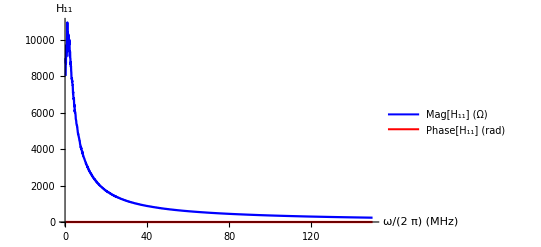

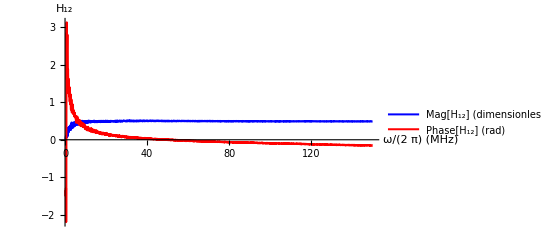

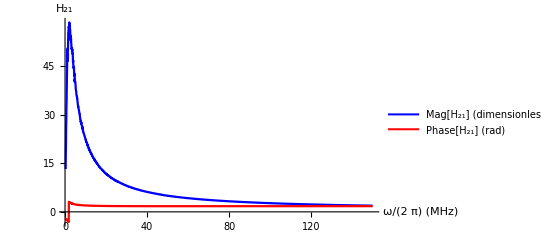

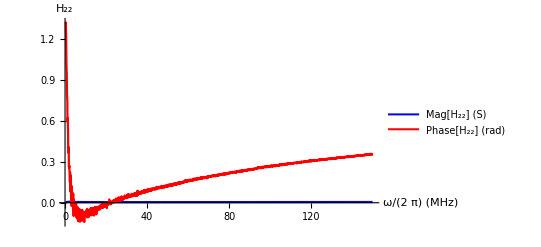

```mathematica
PlotMnmFunctionMagPhase[ArrayFrequencies[[1]],ArrayHMatrices[[1]],"H_11",1,1,"(Ω)"] (* Plotting Subscript[H, 11] *) 
PlotMnmFunctionMagPhase[ArrayFrequencies[[1]],ArrayHMatrices[[1]],"H_12",1,2,"(dimensionless)"] (* Plotting Subscript[H, 12] *) 
PlotMnmFunctionMagPhase[ArrayFrequencies[[1]],ArrayHMatrices[[1]],"H_21",2,1,"(dimensionless)"] (* Plotting Subscript[H, 21] *) 
PlotMnmFunctionMagPhase[ArrayFrequencies[[1]],ArrayHMatrices[[1]],"H_22",2,2,"(S)"] (* Plotting Subscript[H, 22] *)
```

#### 6.2.5 Plotting the G-parameters (inverse hybrid parameters)

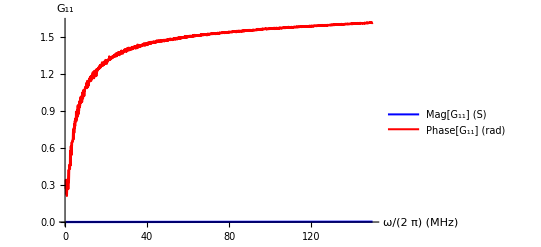

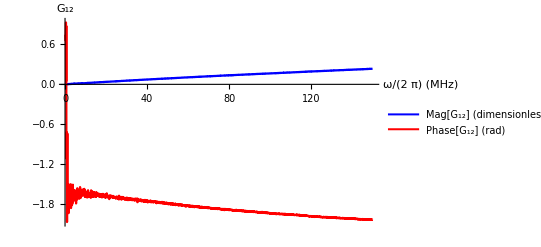

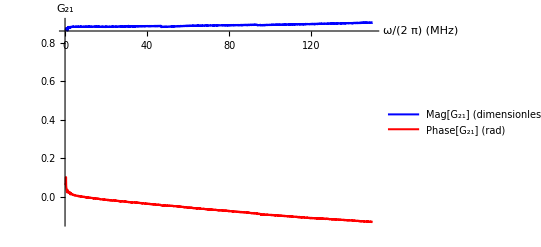

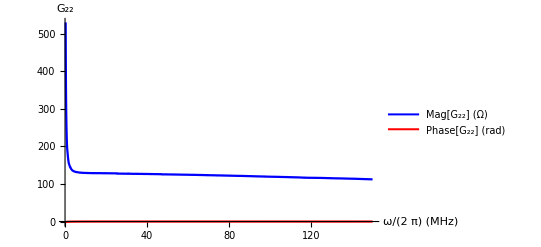

```mathematica
PlotMnmFunctionMagPhase[ArrayFrequencies[[1]],ArrayGMatrices[[1]],"G_11",1,1,"(S)"] (* Plotting Subscript[G, 11] *) 
PlotMnmFunctionMagPhase[ArrayFrequencies[[1]],ArrayGMatrices[[1]],"G_12",1,2,"(dimensionless)"] (* Plotting Subscript[G, 12] *) 
PlotMnmFunctionMagPhase[ArrayFrequencies[[1]],ArrayGMatrices[[1]],"G_21",2,1,"(dimensionless)"] (* Plotting Subscript[G, 21] *) 
PlotMnmFunctionMagPhase[ArrayFrequencies[[1]],ArrayGMatrices[[1]],"G_22",2,2,"(Ω)"] (* Plotting Subscript[G, 22] *)
```